Entanglement generation between nodes separated by d km with cavities.
Fixed parameters:
Speed of light in optical fibre at telecom in km/μs:

```mathematica
c = 0.2;
```

Losses: 0.2 dB/km.

Variables:
d - separation between nodes in km
pfc - Probability of successful frequency conversion
pout - outcoupling efficiency
Eg - time of generating spin photon entanglement in μs.
Sg - time of the swap gate between the nuclear and electron spin in μs.
PurGat - time of the controlled not gate for purification and the measurement on the target pair
pm - probability that the SPDC source emits entangled photons
n - number of memories (including the electron spin as a memory)

Probability that a photon will survive over the distance of d/2 km (with 0.2 dB losses/km):

```mathematica
Ploss[d_] := 10^(-0.2 d/20);
```

Probability that if one photon got emitted from the NV, it will be collected, successfully converted to telecom and it successfully arrives at the BS:

```mathematica
P[d_,pfc_,pout_] := Ploss[d]*pfc*pout;
```

```mathematica
MinDistanceForNMemories[n_,Eg_,Sg_]:=c((n-1)(Eg +Sg) +Eg);
MaxMemoriesForDistance[d_,Eg_,Sg_]:=(d/c-Eg)/(Eg +Sg)+1
```

#### Repeated Barrett and Kok with n nuclear spins:

Probability that a single run of Barrett and Kok scheme succeeds (two consecutive attempts succeed, 2 photons detected):

```mathematica
PBK[d_,pfc_,pout_]  := 1/2 P[d,pfc,pout]^2;
```

Probability of success of a single run of the protocol (try n times, swap first n-1 attempts to nuclear spins, the nth one stays on electron spins [for d=50km, generation of spin photon entanglement + roundtrip of a photon [in total around 10^(-4)s] is much shorter than the T2 of the NV, so the last state can be stored in NV]):

Probability that the protocol succeeds:

```mathematica
PnBK[n_,d_,pfc_,pout_] := 1 - (1-PBK[d,pfc,pout])^n;
```

Added by PH for later use: Probability that the protocol generates m pairs:

```mathematica
PmBK[n_,m_,d_,pfc_,pout_] := Binomial[n,m] PBK[d,pfc,pout]^m(1-PBK[d,pfc,pout])^(n-m);
```

Duration of one attempt of the protocol in μs (performing Barrett and Kok n times with swapping to the nuclear spin after each Barrett and Kok run (apart from the last one), at the end we wait until the message comes back to the node with success/failure info):

Modified by PH

```mathematica
TnBK[n_,Eg_,d_, Sg_] :=Max[ (n-1)*(Eg +Sg) + Eg,   d/c];
```

Average rate (number of generated pairs per μs):

```mathematica
RatenBK[n_,d_,pfc_,pout_,Eg_,Sg_] := PnBK[n,d,pfc,pout]/TnBK[n,Eg,d,Sg];
```

Rate assuming that we can generate more than one copy per each round of the protocol:

```mathematica
RatenBK2[n_,d_,pfc_,pout_,Eg_,Sg_] := (n*PBK[d,pfc,pout])/TnBK[n,Eg,d,Sg];
```

Decoherence can only occur during a single round, since we try n times and might have gotten a click before the last attempt

```mathematica
AvgFidelityBnK[n_,mLt_]:=Mean[Table[Exp[-(n-x)/mLt],{x,1,n}]];
```

#### Purification scheme with n nuclear spins:

Again we can try n times:

Probability of a single click (half of the times from the required 0-1 or 1-0 photon case, 1/4 of the times we have the 1-1 case when one of the photon could get lost):

```mathematica
PSC[d_,pfc_,pout_]  := 1/2 P[d,pfc,pout] + 1/4*2P[d,pfc,pout]*(1-P[d,pfc,pout]);
```

Probability of generating one pair in a single run of the protocol:

```mathematica
PnSC[n_,d_,pfc_,pout_] := 1-(1-PSC[d,pfc,pout] )^n;
```

Duration of the first part of the protocol (no purification)

```mathematica
TnNoPur[n_,Eg_,d_, Sg_] := Max[(n-1)*(Eg +Sg) + Eg,d/c];
```

PH- I don’t think this should be a duration for any reasonable protocol, since would definitely keep going while found out if succeeded, but fine, we can keep it in for now. Duration of applying purification:

```mathematica
Tpur[d_,PurGat_] := PurGat + d/c;
```

Average time of the protocol (limit of only one click at most per round):

```mathematica
TnPur[n_,d_,pfc_,pout_,Eg_, Sg_,PurGat_] := TnNoPur[n,Eg,d, Sg]/PnSC[n,d,pfc,pout]+ TnNoPur[n-1,Eg,d, Sg]/PnSC[n-1,d,pfc,pout]+ Tpur[d,PurGat];
```

Rate:

```mathematica
RatenPur[n_,d_,pfc_,pout_,Eg_,Sg_,PurGat_] :=If[n≥ 2,(1/8)/TnPur[n,d,pfc,pout,Eg, Sg,PurGat],0];
```

Once get a click, need to store in memory while get next click. Calculate avg fidelity after this by determining prob of succeeding for second click gen in round k. Decoherence at this point is k n times decoherence per round

```mathematica
AvgFidelitynPur[n_,d_,pfc_,pout_,mLt_]:=If[n≥2,Sum[PnSC[n-1,d,pfc,pout](1-PnSC[n-1,d,pfc,pout])^(k-1)Exp[-(k (n-1))/mLt],{k,1,∞}],None]
```

Notice that this is approx Sum[(1-Psc)^((n-1) (k-1))(n-1)Psc Exp[-k(n-1)/tau],{k,1,∞}] which is approx equiv to Sum[(1-Psc)^(x-1)Psc Exp[-x/tau],{x,1,∞}] by subbing x = (n-1) (k), and assuming that 1/psc and tau are both much bigger than n (so that the terms dont change very much from x = (n-1)(k-1) to (n-1)k, allowing us to approximate the n times by the sum of the n terms from n(k-1) to nk. What this is saying is that in essence, all that matters is the number of attempts required to get a single click - multiplexing simply makes this happen faster.

This makes it somewhat simple to bound the number of attempts for a given fidelity. I calculated FullSimplify[Sum[p(1-p)^(n-1)Exp[-n/τ],{n,1,m}]/Sum[p(1-p)^(n-1),{n,1,m}]], and then simplified by hand (with approxes) to get (1-ⅇ^(-m/τ)(1-p)^m)/((1-(1-p)^m) (1/(p τ)+1)). Although since NSolve, actually just put original expression back in

```mathematica
AvgFidelitynPurBoundedAttempts[n_,d_,pfc_,pout_,mLt_,maxAttempts_]:=If[n≥2,Sum[PnSC[n-1,d,pfc,pout](1-PnSC[n-1,d,pfc,pout])^(k-1)Exp[-(k (n-1))/mLt],{k,1,maxAttempts}]/Sum[PnSC[n-1,d,pfc,pout](1-PnSC[n-1,d,pfc,pout])^(k-1),{k,1,maxAttempts}],None]
```

```mathematica
MaxAttemptsSecondRoundPurification[Fid_,mLt_,n_,d_,pfc_,pout_]:=If[AvgFidelitynPur[n,d,pfc,pout,mLt]≥Fid,∞,FindArgMin[Abs[AvgFidelitynPurBoundedAttempts[n,d,pfc,pout,mLt,m]-Fid],m,Method->"PrincipalAxis"][[1]]]
```

```mathematica
AvgAttemptsPurBounded[n_,d_,pfc_,pout_,mLt_,maxAttempts_]:=Sum[k PnSC[n-1,d,pfc,pout](1-PnSC[n-1,d,pfc,pout])^(k-1),{k,1,maxAttempts}]/Sum[PnSC[n-1,d,pfc,pout](1-PnSC[n-1,d,pfc,pout])^(k-1),{k,1,maxAttempts}]
```

So, if we limit the attempts to this number, we need to recalculate the rate.

Average time of the protocol (limit of only one click at most per round):

```mathematica
ProbSuccessSecondRound[maxAttempts_,n_,d_,pfc_,pout_] :=1-(1-PSC[d,pfc,pout])^((n-1)maxAttempts);
TnPurBoundedFid[n_,d_,pfc_,pout_,Eg_, Sg_,PurGat_,mLt_,maxAttempts_] := 1/ProbSuccessSecondRound[maxAttempts,n,d,pfc,pout](TnNoPur[n,Eg,d, Sg]/PnSC[n,d,pfc,pout]+ AvgAttemptsPurBounded[n,d,pfc,pout,mLt,maxAttempts] TnNoPur[n-1,Eg,d, Sg]) + Tpur[d,PurGat];
```

Rate:

```mathematica
RatenPurBounded[n_,d_,pfc_,pout_,Eg_,Sg_,PurGat_,mLt_,Fid_] :=If[n≥ 2,1/8/TnPurBoundedFid[n,d,pfc,pout,Eg, Sg,PurGat,mLt,MaxAttemptsSecondRoundPurification[Fid,mLt,n,d,pfc,pout]],0];
```

Idiot check that this gives the expected fidelity:

```mathematica
AvgFidelitynPurBounded[n_,d_,pfc_,pout_,mLt_,Fid_]:=AvgFidelitynPurBoundedAttempts[n,d,pfc,pout,mLt,MaxAttemptsSecondRoundPurification[Fid,mLt,n,d,pfc,pout]]
```

#### Kwiat protocol

Quoting from Kwiat paper:

Probability that the left photon is latched into NV:

```mathematica
pl[d_,pfc_,pout_] := 1/2 P[d,pfc,pout];
```

Probability of generating entanglement between the first set of memory qubits? The Kwiat formula is only valid if entanglement generation rate is much much faster than the communication time. Dont want any overhead in time.

```mathematica
pBothSidesPerRound[d_,pfc_,pout_,pm_]:=pl[d,pfc,pout]^2 *pm;
pent[d_,pfc_,pout_,pm_ ,n_,Eg_,Sg_ ,maxAttempts_] := Sum[ pBothSidesPerRound[d,pfc,pout,pm]*(1 - 2pm pl[d,pfc,pout] + pBothSidesPerRound[d,pfc,pout,pm])^(k-1),{k,1,maxAttempts}];
(*pent[d_,pfc_,pout_,pm_ ,n_,Eg_,Sg_] :=pl[d,pfc,pout]/2; Kwiat expression*)
```

It is optimal (I think) to use as many memories as possible, and have as little dead as time as possible (at least as far as the rate is concerned). This is true up until the point at which very likely to have already generated a click on each side.

```mathematica
MaxAttemptsPerBlock [d_,n_,Eg_,Sg_,pm_,pfc_,pout_]:=Max[Min[ (d/c)/(n Eg) ,3/ProbPerAttempt[pm,d,pfc,pout]],1];
(*MaxAttemptsPerBlock [d_,n_,Eg_,Sg_,pm_,pfc_,pout_]:=3/ProbPerAttempt[pm,d,pfc,pout]; Kwiat expression *)
```

Average time after which the first photon got latched on both sides:

```mathematica
Tplatched[Eg_,d_,pfc_,pout_,pm_]:=Eg/(pm pl[d,pfc,pout]);
```

Duration of the whole protocol (applying this procedure n times, n-1 times swapping to nuclear spin and waiting for results from the other side at the end).

```mathematica
TKwiatwhole[n_,d_,pfc_,pout_,Eg_,Sg_,pm_,maxAttempts_]  :=Max[n Eg maxAttempts+ (n-1)Sg ProbPerBlock[pm,d,pfc,pout,n,Eg,Sg,maxAttempts] ,d/c];
```

Rate:

```mathematica
RateKwiat[n_,d_,pfc_,pout_,Eg_,Sg_,pm_]:= (1-(1-pent[d,pfc,pout,pm ,n,Eg,Sg,MaxAttemptsPerBlock[d,n,Eg,Sg,pm,pfc,pout]])^n)/TKwiatwhole[n,d,pfc,pout,Eg,Sg,pm,MaxAttemptsPerBlock[d,n,Eg,Sg,pm,pfc,pout]];
```

Rate assuming that we can generate more than one copy per round of the protocol

```mathematica
RateKwiat2[n_,d_,pfc_,pout_,Eg_,Sg_,pm_]:= (n*pent[d,pfc,pout,pm ,n,Eg,Sg,MaxAttemptsPerBlock[d,n,Eg,Sg,pm,pfc,pout]])/TKwiatwhole[n,d,pfc,pout,Eg,Sg,pm,MaxAttemptsPerBlock[d,n,Eg,Sg,pm,pfc,pout]];
```

```mathematica
ProbPerAttempt[pm_,d_,pfc_,pout_] :=pm pl[d,pfc,pout];
ProbPerBlock[pm_,d_,pfc_,pout_,n_,Eg_,Sg_,maxAttempts_]:=Sum[ProbPerAttempt[pm,d,pfc,pout](1-ProbPerAttempt[pm,d,pfc,pout] )^(k-1),{k,1,maxAttempts}];
MeanAttemptsPerBlock[pm_,d_,pfc_,pout_,n_,Eg_,Sg_ ,maxAttempts_]:=Sum[k ProbPerAttempt[pm,d,pfc,pout](1-ProbPerAttempt[pm,d,pfc,pout] )^(k-1),{k,1,maxAttempts}]/ProbPerBlock[pm,d,pfc,pout,n,Eg,Sg,maxAttempts];
AvgFidelityKwiat[n_,d_,pfc_,pout_,pm_,n_,Eg_,Sg_,mLt_]:=Mean[Table[Exp[-((x-1)MeanAttemptsPerBlock[pm,d,pfc,pout,n,Eg,Sg,MaxAttemptsPerBlock[d,n,Eg,Sg,pm,pfc,pout]])/mLt],{x,1,n}]];
```

Bound the fidelity

```mathematica
AvgFidelityKwiatBoundedAttempts[n_,d_,pfc_,pout_,pm_,n_,Eg_,Sg_,mLt_,maxAttempts_]:=Mean[Table[Exp[-((x-1)MeanAttemptsPerBlock[pm,d,pfc,pout,n,Eg,Sg,maxAttempts])/mLt],{x,1,n}]];
```

```mathematica
MaxAttemptsPerBlockBounded[Fid_,n_,d_,pfc_,pout_,pm_,n_,Eg_,Sg_,mLt_]:=If[AvgFidelityKwiat[n,d,pfc,pout,pm,n,Eg,Sg,mLt]≥Fid,MaxAttemptsPerBlock[d,n,Eg,Sg,pm,pfc,pout],FindArgMin[Abs[AvgFidelityKwiatBoundedAttempts[n,d,pfc,pout,pm,n,Eg,Sg,mLt,m]-Fid],m,Method->"PrincipalAxis"][[1]]]
```

```mathematica
RateKwiatBounded[n_,d_,pfc_,pout_,Eg_,Sg_,pm_,mLt_,Fid_]:= (1-(1-pent[d,pfc,pout,pm ,n,Eg,Sg,MaxAttemptsPerBlockBounded[Fid,n,d,pfc,pout,pm,n,Eg,Sg,mLt]])^n )/TKwiatwhole[n,d,pfc,pout,Eg,Sg,pm,MaxAttemptsPerBlockBounded[Fid,n,d,pfc,pout,pm,n,Eg,Sg,mLt]];
```

```mathematica
AvgFidelityKwiatBounded[n_,d_,pfc_,pout_,pm_,n_,Eg_,Sg_,mLt_,Fid_]:=AvgFidelityKwiatBoundedAttempts[n,d,pfc,pout,pm,n,Eg,Sg,mLt,MaxAttemptsPerBlockBounded[Fid,n,d,pfc,pout,pm,n,Eg,Sg,mLt]]
```

```mathematica
Module[{m,Fid,n,pfc,pout,pm,d,mLt,Eg,Sg,PurGat,RateData,FidData},
pfc=0.3;
pout=0.3;
pm=0.1;
mLt=400;
Eg=1;
Sg=20;
PurGat=10;
n=4; 
Fid=0.9;
d=47;
FindArgMin[Abs[AvgFidelityKwiatBoundedAttempts[n,d,pfc,pout,pm,n,Eg,Sg,mLt,m]-Fid],m,Method->"PrincipalAxis"]]
```

{57.7884}

#### Plots

```mathematica
Module[{n,pfc,pout,pm,mLt,Eg,Sg,PurGat,MinFid,RateData,FidData},
pfc=0.3;
pout=0.3;
pm=0.1;
mLt=400;
Eg=1;
Sg=20;
PurGat=10;
n=4; 
MinFid=0.9;
RateData=Transpose[Table[{{d,10^6 RateKwiatBounded[n,d,pfc,pout,Eg,Sg,pm,mLt,MinFid] },{d,10^6 RatenBK[n,d,pfc,pout,Eg,Sg]},{d,10^6 RatenPurBounded[n,d,pfc,pout,Eg,Sg,PurGat,mLt,MinFid]},{d,10^6 RateKwiat[n,d,pfc,pout,Eg,Sg,pm] },{d,10^6 RatenPur[n,d,pfc,pout,Eg,Sg,PurGat]  }},{d,0,100,20}]];
FidData=Transpose[Table[{{d,AvgFidelityKwiatBounded[n,d,pfc,pout,pm,n,Eg,Sg,mLt,MinFid] },{d,AvgFidelityBnK[n,mLt]},{d,AvgFidelitynPurBounded[n,d,pfc,pout,mLt,MinFid]},{d,AvgFidelityKwiat[n,d,pfc,pout,pm,n,Eg,Sg,mLt] },{d,AvgFidelitynPur[n,d,pfc,pout,mLt]}},{d,0,100,20}]];
plotRateWDistance=ListLogPlot[RateData,Frame->True,Joined->True,AxesOrigin->{0,Automatic},Epilog->{Directive[Red,Dashed],Line[{{ MinDistanceForNMemories[n,Eg,Sg],-100},{MinDistanceForNMemories[n,Eg,Sg],1*^6}}]},PlotLegends->{"Kwiat","BK","Pur"}, FrameLabel->{"Node sep. (km)","Rate (Hz)"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[3]],Dashed]},BaseStyle->{FontSize->12},ImageSize->400];
plotFidelityWDistance=ListPlot[FidData,BaseStyle->{FontSize->12},AxesOrigin->{0,Automatic},Epilog->{Directive[Red,Dashed],Line[{{ MinDistanceForNMemories[n,Eg,Sg],-100},{MinDistanceForNMemories[n,Eg,Sg],1*^6}}]},PlotLegends->{"Kwiat", "BK","Pur"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[3]],Dashed]}, Frame->True,Joined->True,FrameLabel->{"Node sep. (km)","Avg. fidelity"},ImageSize->400];
]
```

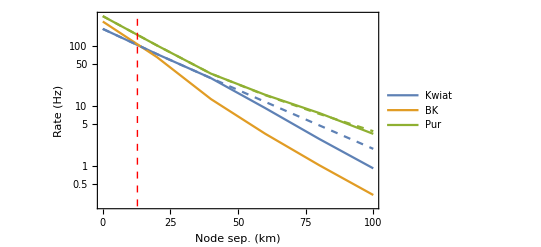

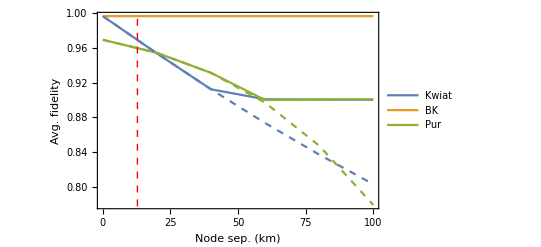

```mathematica
plotRateWDistance
plotFidelityWDistance
```

#### Current params (w. cavity since necessary)

```mathematica
Module[{n,pfc,pout,pm,mLt,Eg,Sg,PurGat,MinFid,RateData,FidData},
pfc=0.1;
pout=0.1;
pm=0.01;
mLt=200;
Eg=2;
Sg=200;
PurGat=100;
n=3; 
MinFid=0.9;
RateData=Transpose[Table[{{d,10^6 RateKwiatBounded[n,d,pfc,pout,Eg,Sg,pm,mLt,MinFid] },{d,10^6 RatenBK[n,d,pfc,pout,Eg,Sg]},{d,10^6 RatenPurBounded[n,d,pfc,pout,Eg,Sg,PurGat,mLt,MinFid]},{d,10^6 RateKwiat[n,d,pfc,pout,Eg,Sg,pm] },{d,10^6 RatenPur[n,d,pfc,pout,Eg,Sg,PurGat]  }},{d,0,100,20}]];
FidData=Transpose[Table[{{d,AvgFidelityKwiatBounded[n,d,pfc,pout,pm,n,Eg,Sg,mLt,MinFid] },{d,AvgFidelityBnK[n,mLt]},{d,AvgFidelitynPurBounded[n,d,pfc,pout,mLt,MinFid]},{d,AvgFidelityKwiat[n,d,pfc,pout,pm,n,Eg,Sg,mLt] },{d,AvgFidelitynPur[n,d,pfc,pout,mLt]}},{d,0,100,20}]];
plotRateWDistance=ListLogPlot[RateData,Frame->True,Joined->True,AxesOrigin->{0,Automatic},Epilog->{Directive[Red,Dashed],Line[{{ MinDistanceForNMemories[n,Eg,Sg],-100},{MinDistanceForNMemories[n,Eg,Sg],1*^6}}]},PlotLegends->{"Kwiat","BK","Pur"}, FrameLabel->{"Node sep. (km)","Rate (Hz)"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[3]],Dashed]},BaseStyle->{FontSize->12},ImageSize->400];
plotFidelityWDistance=ListPlot[FidData,BaseStyle->{FontSize->12},AxesOrigin->{0,Automatic},Epilog->{Directive[Red,Dashed],Line[{{ MinDistanceForNMemories[n,Eg,Sg],-100},{MinDistanceForNMemories[n,Eg,Sg],1*^6}}]},PlotLegends->{"Kwiat", "BK","Pur"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[3]],Dashed]}, Frame->True,Joined->True,FrameLabel->{"Node sep. (km)","Avg. fidelity"},ImageSize->400];
]
```

FindArgMin::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

General::stop: Further output of FindArgMin::fmmp will be suppressed during this calculation.

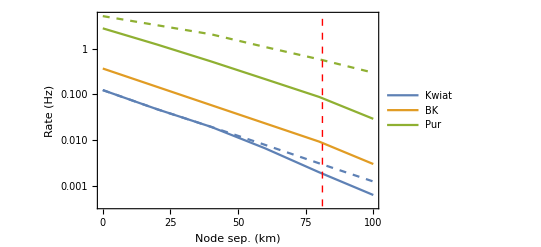

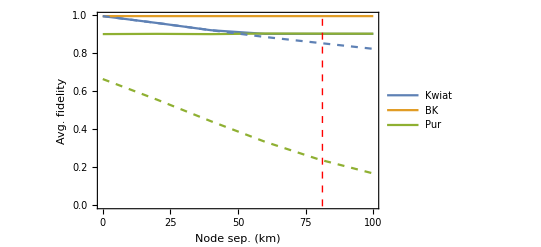

```mathematica
plotRateWDistance
plotFidelityWDistance
```

#### Fixed distance, changing n

```mathematica
Module[{d,pfc,pout,pm,mLt,Eg,Sg,PurGat,MinFid,RateData,FidData},
pfc=0.3;
pout=0.3;
pm=0.1;
mLt=400;
Eg=1;
Sg=20;
PurGat=10;
d=50; 
MinFid=0.9;
RateData=Transpose[Table[{{n,10^6 RateKwiatBounded[n,d,pfc,pout,Eg,Sg,pm,mLt,MinFid] },{n,10^6 RatenBK[n,d,pfc,pout,Eg,Sg]},{n,10^6 RatenPurBounded[n,d,pfc,pout,Eg,Sg,PurGat,mLt,MinFid]},{n,10^6 RateKwiat[n,d,pfc,pout,Eg,Sg,pm] },{n,10^6 RatenPur[n,d,pfc,pout,Eg,Sg,PurGat]  }},{n,1,8}]];
FidData=Transpose[Table[{{n,AvgFidelityKwiatBounded[n,d,pfc,pout,pm,n,Eg,Sg,mLt,MinFid] },{n,AvgFidelityBnK[n,mLt]},{n,AvgFidelitynPurBounded[n,d,pfc,pout,mLt,MinFid]},{n,AvgFidelityKwiat[n,d,pfc,pout,pm,n,Eg,Sg,mLt] },{n,AvgFidelitynPur[n,d,pfc,pout,mLt]}},{n,1,8}]];
plotRateWNMemories=ListLogPlot[RateData,Frame->True,Joined->True,AxesOrigin->{0,Automatic},Epilog->{Directive[Red,Dashed],Line[{{ MaxMemoriesForDistance[d,Eg,Sg],-100},{MaxMemoriesForDistance[d,Eg,Sg],1*^6}}]},PlotLegends->{"Kwiat","BK","Pur"}, FrameLabel->{"Number of memories (inc. e)","Rate (Hz)"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[3]],Dashed]},BaseStyle->{FontSize->12},ImageSize->400];
plotFidelityWNMemories=ListPlot[FidData,BaseStyle->{FontSize->12},AxesOrigin->{0,Automatic},Epilog->{Directive[Red,Dashed],Line[{{ MaxMemoriesForDistance[d,Eg,Sg],-100},{MaxMemoriesForDistance[d,Eg,Sg],1*^6}}]},PlotLegends->{"Kwiat", "BK","Pur"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[3]],Dashed]}, Frame->True,Joined->True,FrameLabel->{"Number of memories (inc. e)","Avg. fidelity"},ImageSize->400];
]
```

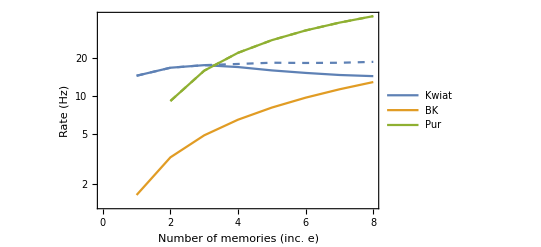

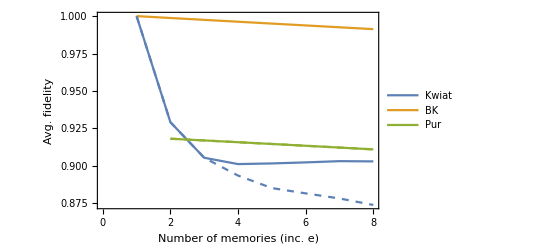

```mathematica
plotRateWNMemories
plotFidelityWNMemories
```